```mathematica
Off[General::munfl]
```

#### Load force profiles, and set parameters and conversions

```mathematica
fname32="C:/Users/Christian/Desktop/CaOCH3Data/uploaded_files/ptsJ32Jp12_IntensityScan_Cooling.csv";(*file path for force profiles must be changed accordingly*)
isat=Quantity[2.4,"Milliwatts"/("Centimeters")^2]*1.2;(*simple rate analysis suggests a correction factor 2ng/(ne+ng)=3/2 due to multi-level structure; we here find 1.2 appropriate*) 
mCaOCH3=(Entity["Element","Calcium"][EntityProperty["Element","AtomicMass"]] + Entity["Element","Oxygen"][EntityProperty["Element","AtomicMass"]] + Entity["Element","Carbon"][EntityProperty["Element","AtomicMass"]]+3 Entity["Element","Hydrogen"][EntityProperty["Element","AtomicMass"]]);(*mass of molecule*)
tdecay=Quantity[35, "Nanoseconds"];
vrecoil=QuantityMagnitude@UnitConvert[Quantity[, "PlanckConstant"]/λ/mCaOCH3];
ftoa=QuantityMagnitude@UnitConvert@((Quantity[, "ReducedPlanckConstant"]((2π)/λ)(1/tdecay))/mCaOCH3);(*conversion between force and acceleration: m/s^2*)
rtor=QuantityMagnitude@UnitConvert@(1/tdecay);(*factor for scattering rate: MHz*)
vtov=QuantityMagnitude@UnitConvert@(((1/tdecay))/((2π)/λ));(*factor for velocity: m/s*)
βtoB=QuantityMagnitude@(UnitConvert[(Quantity[, "ReducedPlanckConstant"](1/tdecay)/Quantity[, "BohrMagneton"]),"Gauss"]);(*factor for B field: m/s*)
(*cooling beam parameters*)
λ=Quantity[629.483,"Nanometers"];(*wavelength of cooling light*)
dFWHM=0.001(3.14+3.63)/2;(*FWHM diameter of cooling beam (mm)*)
waist=dFWHM/√(2Log[2])(*waist of cooling beam*);
Clear@intensity
intensity[x_,y_]:=Exp[-2(x^2+y^2)/waist^2]/QuantityMagnitude[isat]
```

### Load force data

```mathematica
rawdata=Import[fname32,"CSV",HeaderLines->1];
indices = DeleteCases[
Table[If[rawdata[[i,1;;4]]!=rawdata[[i+1,1;;4]],i,None],{i,Length@rawdata-1}],
None];
data=Append[rawdata[[indices]],rawdata[[-1]]];
data = Select[data,#[[4]]≠0&];
data=Join[data,(data/.{a_,b_,c_,d_,e_,f_}->{a,b,c,-d,-e,f})];
Bs=βtoB data[[;;,1]];
s0s=data[[;;,2]];
Δs=data[[;;,3]];
vs=vtov data[[;;,4]];
as=ftoa data[[;;,5]];
rs=rtor data[[;;,6]];
ainterp32= Interpolation[#,InterpolationOrder->1,"ExtrapolationHandler"->{(0.0&),"WarningMessage"->False}]&@Table[{{Bs[[i]],s0s[[i]],Δs[[i]],vs[[i]]},as[[i]]},{i,Length@data}];
rinterp32= Interpolation[#,InterpolationOrder->1,"ExtrapolationHandler"->{(0.0&),"WarningMessage"->False}]&@Table[{{Bs[[i]],s0s[[i]],Δs[[i]],vs[[i]]},rs[[i]]},{i,Length@data}];
```

#### Define function to initialize particles

```mathematica
InitializeParticles[nparticles_,daperture_,dcell_,zaperture_,vzmin_,vzavg_,vzstd_,vxstd_, zcool_,xstd_]:=ParallelTable[Module[{vzinit,vxinit,vyinit,xinit=daperture+dcell+1,yinit=daperture+dcell+1},
While[Abs[xinit] > daperture/2 || Abs[yinit] > daperture/2,
(*Create particles at cell*)
vzinit=Map[Max[vzmin,#]&,RandomVariate[NormalDistribution[vzavg, vzstd]]];
vxinit=RandomVariate[NormalDistribution[0, vxstd]];
vyinit=RandomVariate[NormalDistribution[0, vxstd]];
xinit=RandomVariate[NormalDistribution[0, xstd]];
yinit=RandomVariate[NormalDistribution[0, xstd]];
(*Propagate to aperture*)
xinit+=vxinit*(zaperture/vzinit);
yinit+=vyinit*(zaperture/vzinit);
];
(*propagate to start of cooling region*)
xinit+=vxinit zcool/vzinit;
yinit+=vyinit zcool/vzinit;
{xinit,vxinit,vzinit,yinit,vyinit}],
{i,nparticles},Method->"CoarsestGrained"]
```

#### Define function to simulate trajectories

```mathematica
SimulateTrajectoryFast[{x0_,vx0_,vz_,y0_,vy_},β_,p_,Δ_,nscatteravg_]:=Module[{eqns,tmax,tend,sol,nscatter},
nscatter=RandomVariate[ExponentialDistribution[1/nscatteravg]];
tmax=lcool/vz;
decayed=0;
eqns={
vx[0]==vx0,
x[0]==x0,
n[0]==0,
vx'[t]==ainterp[β,p intensity[vz t-lcool/2, y0+vy t],Δ,vx[t]],
x'[t]==vx[t],
n'[t]==rinterp[β,p intensity[vz t-lcool/2, y0+vy t],Δ,vx[t]],
WhenEvent[n[t]>nscatter,"StopIntegration"],
WhenEvent[Mod[n[t],1]>0.5,vx[t]->vx[t]+RandomReal[{-vrecoil,vrecoil}]],
WhenEvent[n[t]>nscatter, decayed=1]
};
sol=First@NDSolve[eqns,{x,vx,n},{t,0,tmax},
AccuracyGoal->5,
PrecisionGoal->3];
tend=(x["Domain"]/.sol)[[1,2]];
{x[tend]+vx[tend]*(tmax - tend + zdetector/vz),vx[tend],tmax-tend,n[tend],decayed,x[0],vx[0],y0,vy,vz}/.sol
]
```

#### Initialize beam with experimental parameters

```mathematica
nparticles=10000;
```

```mathematica
(*constants parameterizing the experiment.
The beam propagates along the z axis.The x axis is the transverse direction. *)
dcell=0.0115;(* Width of cell exit;m*)
vzavg=150.0;(*Average forward velocity;m/s*)
vzstd=30.0;(*Standard deviation of forward velocity;m/s*)
vzmin=10.0;(*Minimum forward velocity;m/s*)
vxstd=20; (*Standard deviation of transverse velocity;m/s*)
zaperture=0.355;(*Distance from cell to aperture;m*)
daperture=0.003;(*Diameter of aperture;m*)
zcool=0.02; (*Length of cooling region;m*)
lcool=0.01;
zdetector=0.515;(*Distance between end of cooling region and detector; m*)
rdetector=0.015;
xstd=0.0038;
init=InitializeParticles[nparticles,daperture,dcell,zaperture,vzmin,vzavg,vzstd,vxstd, zcool,xstd];
```

```mathematica
Γ=N[QuantityMagnitude[1/(2π*tdecay)]]*10^3;
```

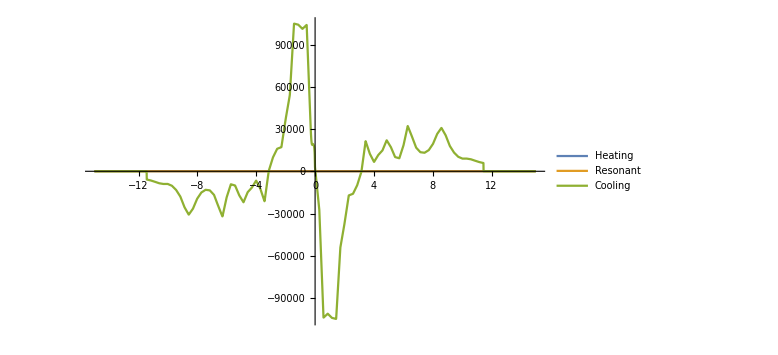

```mathematica
(*visual check of force profiles*)
curves =ainterp32[2.4,QuantityMagnitude[2*800/isat],{-15/Γ,0,25/Γ},v];
Plot[curves,{v,-15,15},ImageSize->Large,PlotLegends->{"Heating","Resonant","Cooling"},PlotRange->All]
```

#### Scan the intensity from 0 to 3000 mW/cm^2

```mathematica
Is=Table[x,{x,0,6000,500}](*power is 2x of that listed in Fig. S6, as intensity defined here is peak intensity, whereas that given in paper is average intensity*)
```

{0,500,1000,1500,2000,2500,3000,3500,4000,4500,5000,5500,6000}

```mathematica
FScale=0.5;(*simple rate analysis suggests a correction factor 2ne/(ne+ng)=1/2 due to multi-level structure*)
```

```mathematica
ainterp[a_,b_,c_,d_]:=ainterp32[a,b,c,d]*FScale*0.625;(*compute the lower bound, corresponding to a 0.625 times smaller force (~50 rather than ~80 photons)*)
rinterp[a_,b_,c_,d_]:=rinterp32[a,b,c,d]*FScale*0.625;
```

```mathematica
images1={};
Do[
First@AbsoluteTiming[cooled=ParallelMap[SimulateTrajectoryFast[#,2.4,QuantityMagnitude[2Intensity/isat],25/Γ,50]&,init]];(*arguments for simulating trajectories are: B-field, intensity (2x for two laser beams), detuning, and average # photons scattered*)
Mean[cooled[[;;,4]]];
cooledf=Select[cooled,#[[5]]==0&];
cooledimaged=Select[cooledf,Abs[#[[1]]]<rdetector&];AppendTo[images1,cooledimaged];
c1=Length[cooledimaged];
Print[SmoothHistogram[cooledimaged[[;;,1]],0.001,PlotStyle->Blue,ImageSize->Medium,PlotRange->{{-0.015,0.015},{0,150}},Axes->{True,True},ScalingFunctions->{Identity,{#*c1&,#/c1&}}]],
{Intensity,Is}]
```

```mathematica
widths={};(*produce width from beam images*)
Do[
dist=SmoothKernelDistribution[image[[;;,1]],InterpolationPoints->4000];
pdf=PDF[dist];
iF=First[Cases[pdf,_InterpolatingFunction,∞,Heads->True]];
Peaks=Pick[iF["Coordinates"][[1]],PeakDetect[iF["ValuesOnGrid"]],1];
PeakValue=Max[pdf[Peaks]];
GreaterThreshold=Position[pdf[iF["Coordinates"][[1]]],_?(#>PeakValue/Sqrt[E]&)];
totalDist=Last[iF["Coordinates"][[1]]]-First[iF["Coordinates"][[1]]];
left=First[GreaterThreshold][[1]];
right=Last[GreaterThreshold][[1]];diameter=(right-left)*totalDist/4000;
Print[diameter/2];AppendTo[widths,diameter/2],
{image,images1}]
```

```mathematica
ainterp[a_,b_,c_,d_]:=ainterp32[a,b,c,d]*FScale*2.25;(*compute the upper bound, corresponding to a 2.25 larger force (~180 rather than ~80 photons)*)
rinterp[a_,b_,c_,d_]:=rinterp32[a,b,c,d]*FScale*2.25;
```

```mathematica
images2={};
Do[
First@AbsoluteTiming[cooled=ParallelMap[SimulateTrajectoryFast[#,2.4,QuantityMagnitude[2Intensity/isat],25/Γ,180]&,init]];(*2I since there are two beams*)
Mean[cooled[[;;,4]]];
cooledf=Select[cooled,#[[5]]==0&];
cooledimaged=Select[cooledf,Abs[#[[1]]]<rdetector&];AppendTo[images2,cooledimaged];
c1=Length[cooledimaged];
Print[SmoothHistogram[cooledimaged[[;;,1]],0.001,PlotStyle->Blue,ImageSize->Medium,PlotRange->{{-0.015,0.015},{0,150}},Axes->{True,True},ScalingFunctions->{Identity,{#*c1&,#/c1&}}]],
{Intensity,Is}]
```

```mathematica
widths={};(*produce width from beam images*)
Do[
dist=SmoothKernelDistribution[image[[;;,1]],InterpolationPoints->4000];
pdf=PDF[dist];
iF=First[Cases[pdf,_InterpolatingFunction,∞,Heads->True]];
Peaks=Pick[iF["Coordinates"][[1]],PeakDetect[iF["ValuesOnGrid"]],1];
PeakValue=Max[pdf[Peaks]];
GreaterThreshold=Position[pdf[iF["Coordinates"][[1]]],_?(#>PeakValue/Sqrt[E]&)];
totalDist=Last[iF["Coordinates"][[1]]]-First[iF["Coordinates"][[1]]];
left=First[GreaterThreshold][[1]];
right=Last[GreaterThreshold][[1]];diameter=(right-left)*totalDist/4000;
Print[diameter/2];AppendTo[widths,diameter/2],
{image,images2}]
```